```mathematica
Clear["@"];
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear :: wrsym will be suppressed during this calculation.

```mathematica
<<Data`;
<<Matcher`;
<<Classifier`;
```

```mathematica
data=nxrData[-1];
ff=Freq23[];
Dimensions[data]
```

{50,2,6,46}

```mathematica
geteer[s_,tg_,fc_]:=Module[
{pdata,templ},
pdata=s[[All,1]];
templ=s[[All,2]];

EER[pdata,templ,tg,fc,{0,10,0.005}]
];
```

```mathematica
(* there are 23 frequency points*)
```

```mathematica
pd1=data[[All,All,All,{1,2}]];
Dimensions[%]
```

{50,2,6,2}

```mathematica
Flatten[pd1,{{1},{2},{3,4}}];
Dimensions[%]
```

{50,2,12}

23

```mathematica
templ=pd1[[All,1]];
pdata=pd1[[All,2]];
```

```mathematica
tg=ConstantArray[ConstantArray[0,Length[templ]],Length[pdata]];
For[i=1;k=1;n=1,i≤Length[pdata],i++,
For[m=1,m≤1,m++,
tg[[n,k]]=1;
n++;
];
k++;
];
```

```mathematica
(*ee=Reap[For[i=1,i≤Length[data[[1,1,1]]],i=i+2,
pp=Flatten[data[[All,All,All,{i,i+1}]],{{1},{2},{3,4}}];
Sow[Mean[geteer[pp,tg,classifyDist1][[2]]]];
Print[i];]][[2,1]];*)
```

```mathematica
ee=Import["Cache_freqff.mx"];
```

```mathematica
xx=Transpose[{ff,100*ee}];
xx
```

{{34000,15.9796},{37000,14.},{40000,11.9796},{43000,21.9796},{46000,12.},{49000,10.},{52000,10.3469},{55000,11.9796},{58000,12.},{61000,12.},{64000,12.},{67000,12.0408},{70000,12.0204},{73000,12.},{76000,11.9592},{79000,12.0612},{82000,13.8367},{85000,13.8776},{88000,14.0204},{91000,13.5714},{94000,14.0204},{97000,13.9796},{100000,14.}}

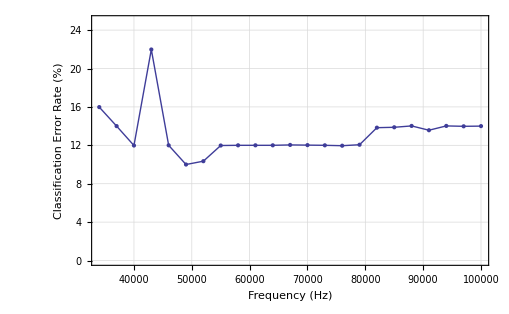

```mathematica
ListPlot[xx,Joined->True,PlotRange->{0,25},Mesh->Full,Axes->False,Frame->True,FrameLabel->{"Frequency (Hz)","Classification Error Rate (%)"},GridLines->Automatic]
```